Uniformly controlled quantum gates, also known as multiplexers, are a class of quantum gates that apply different unitary operations.

Install and load the QuantumFramework paclet:

```mathematica
PacletInstall["Wolfram/QuantumFramework"]
Needs["Wolfram`QuantumFramework`"]
```

Given sequence operators, the number of qubits, n, is set such that 2^n is equal or larger than number of operators. The controlled-gate work as tuples of 0 and 1, for n-qubits.

Multiplexer of two operators:

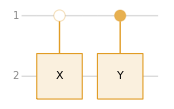

```mathematica
QuantumCircuitOperator[{"Multiplexer","X","Y"}]["Diagram"]
```

Multiplexer of three operators:

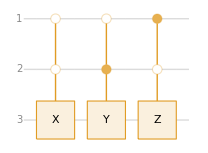

```mathematica
QuantumCircuitOperator[{"Multiplexer","X","Y","Z"}]["Diagram"]
```

Multiplexer of four operators:

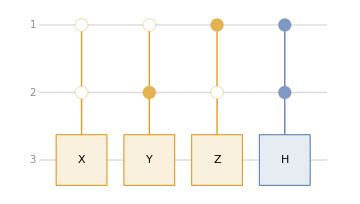

```mathematica
QuantumCircuitOperator[{"Multiplexer","X","Y","Z","H"}]["Diagram"]
```